```mathematica
(*nb1 = NotebookOpen["C:/Users/User/Downloads/4 semestr/CompGeoma/FuntionsFor1.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];*)
```

```mathematica
(*FUNCTIONS*)
PointLocation[{p1_,p2_},p3_]:= Block[{d},d= Det[{p2-p1,p3-p1}];
  If[d>0,Return ["Left"],
If[d<0,Return["Right"],Return["Lie on the line"]]]
];
IsIntersecting[{p1_,p2_},{p3_,p4_}] := Block[{d1,d2,d3,d4}, d1 = Det[{ p4-p3,p1-p3}]; d2 = Det[{p4-p3,p2-p3}]; d3 = Det[{p2-p1,p3-p1}]; d4 = Det[{p2-p1,p4-p1}];
s1=Dot[p3-p1,p4-p1];s2=Dot[p3-p2,p4-p2];s3=Dot[p3-p1,p3-p2];s4=Dot[p4-p1,p4-p2];
If[d1==d2==d3==d4==0 ,
	If[s1 ≤0 || s2 ≤0 || s3≤0 || s4 ≤0,Return[True],Return[False]]
	,If[(d1*d2 ≤ 0)&&(d3*d4≤0),Return[True],Return[False]]
]
];
isPolygonSimple[pts_] := Block[{intersection},intersection = False;
Do[ 
If[i==1, 
Do[
intersection = IsIntersecting[{pts⟦i⟧,pts⟦i+1⟧},{pts⟦j⟧,pts⟦j+1⟧}];
If[intersection == True,Break[]];
,{j,3,n-1}],
Do[
intersection = IsIntersecting[{pts⟦i⟧,pts⟦i+1⟧},{pts⟦j⟧,pts⟦j+1⟧}];
If[intersection == True,Break[]];
,{j,i+2,n}]
]
,{i,1,n-2}
];
If[intersection == True,Return["No"],Return["Yes"]];
];
isConvex[points_] := Block[{counter,check,temp},
counter=0; (*чтобы считать число несовпадений положений*)
If[isPolygonSimple[points] == "No",(*then*)Return["Polygon is not simple"],
(*else*)
check=PointLocation[{points⟦1⟧,points⟦2⟧},points⟦3⟧];(*для того чтобы было с чем сравнить*)
Do[
If[2≤i<n,temp=PointLocation[{points⟦i⟧,points⟦i+1⟧},points⟦i+2⟧],temp=PointLocation[{points⟦i⟧,points⟦i+1⟧},points⟦2⟧]];
If[temp≠check,counter++];
,{i,2,n}
]
];
If[counter==0, Return["Yes"],Return["No, it's concave"]]
];
```

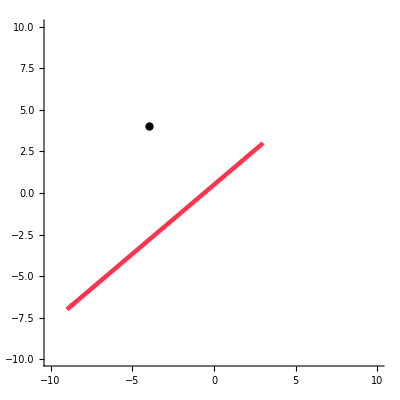

```mathematica
P[n_]:= Table[{RandomInteger[{-10,10}],RandomInteger[{-10,10}]},{n}]
P12 = P[2];
P3= P[1][[1]];
Graphics[{RGBColor[1,0.2,0.3],Thickness[0.008],Arrow[P12],Black,PointSize[0.015],Point[P3]},AspectRatio->Automatic,PlotRange->{{-10,10},{-10,10}},Axes->True]
```

```mathematica
PointLocation[P12,P3]
```

Right

```mathematica
(*TASK 2*)
```

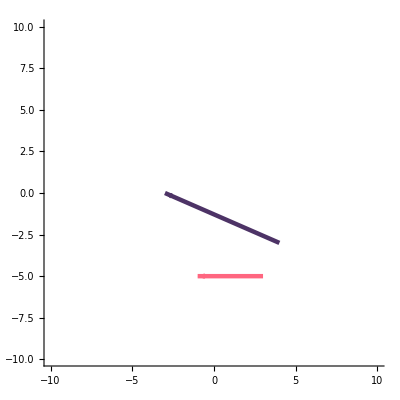

```mathematica
P12 = P[2];
P34 = P[2];
Graphics[{RGBColor[1,0.4,0.5],Thickness[0.008],Arrow[P12],RGBColor[0.3,0.2,0.4],Thickness[0.008],Arrow[P34]},AspectRatio->Automatic,PlotRange->{{-10,10},{-10,10}},Axes->True]
```

```mathematica
If[IsIntersecting[P12,P34] == True,"Intersect","Do not intersect"]
```

Do not intersect

```mathematica
(*TASK 3*)
```

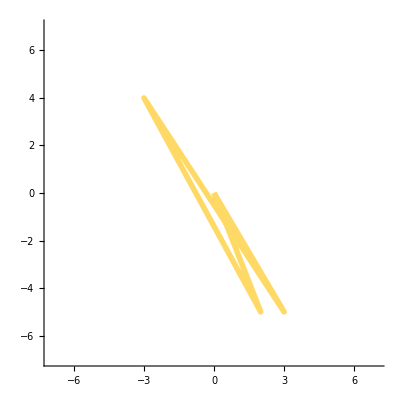

```mathematica
P[n_] := Table[{RandomInteger[{-5,5}],RandomInteger[{-5,5}]},{n}]
n = 4;
pts = Table[P[1][[1]],{i,1,n}];
(*pts={{0,1},{0,-2},{2,0},{2,2},{1,0}}*)
AppendTo[pts,pts⟦1⟧];
Graphics[{RGBColor[1,0.85,0.4],Thickness[0.01],Line[pts]},PlotRange->{{-7,7},{-7,7}},Axes->True]
```

```mathematica
isPolygonSimple[pts]
```

No

```mathematica
(*TASK 4*)
```

```mathematica
isConvex[pts]
```

Polygon is not simple